# Ant Colony Activity

## Sam Keller Physics 234 11/16/2011

## Section 01: Introduction

For most of us, when we think of ants, we think of the insects that can ruin our picnics. They seem to swarm within minutes, amazingly sensing exactly where our food is and already form roads to move our food to their colonies. If we follow these roads back to the colonies, we find a complex structure that contains all sorts of organization, centering around the queen ant, whose sole purpose is to lay eggs. Their colonies are often as deep as they are wide, containing caves upon caves with pathways through it all. The ants themselves  have a number of different jobs: some maintain the nest, some search for food, and some simply sit around and wait for something to do. With their kind of structure, it's easy for one to think that these ants either are strikingly intelligent for their size or they must have a valiant and effective leader^2.

Despite the complexity of ant colonies, neither of these things are true. There are no ants giving out commands for what the rest of the ants should do. No one is in charge. Additionally, individual ants themselves are not smart enough to even comprehend directions or structure. In fact, as Deborah Gordon, a pioneering biologist who specializes in ant activity at Stanford University, said, "If you watch an ant, for any length of time, you're going to end up wanting to help it, because ants are really very inept"^2.  The main question on many scientists minds, then, is how do ant colonies work? Without any manages, and with individuals with little to no brainpower, how do these colonies survive? This simulation is an attempt to begin to understand this organizational feat and to shed light on how simple rules can result in complicated systems.

Studying the patterns of ant colonies has also proved to be a fruitful endeavor in every day applications. Dr. Doug Lawson, a systems analyst at Southwest Airlines, used swam theory-- a theory based on the study of ants that concludes that a group of ants does better than one alone-- to produce a new method for boarding airplanes that's faster than the conventional method. Dr. Lawson assumed that people boarding an airplane are like ants in an ant colony, and since simple rules in an ant colony produce complex systems, Dr. Lawson thought that an efficient boarding process could be produced by some simple rules. It turns out he was correct; Southwest now, instead of giving you an assigned seat, boards their planes with open seating, and their board times are on average faster than the assigned seating method. Because people are likely to take any other seat than the middle seat (this is the simple rule), rarely does a passenger ever need more than one person to get up so they can get to a seat. With assigned seats, however, there's a one in three chance that a passenger needs to ask two people to get up so they can get to their seat, which greatly increases boarding times^4.

Clearly, despite the lack of intelligence of individual ants and their lack of a central authoritative body, ants are still able to produce organized colonies. The reason for this, as we will see, has to do with their ability to use a few simple rules with how they relate to each other to govern their behavior. The results could have great implications for other organizational problems in society!

## Ant Colony Rules

Here we can set up the initial skeleton for an ant colony. All of these rules were adapted from the book titled "Modeling Nature" by Gaylord and Nishidate.

First, we need to explain how exactly we're going to model ants with computers. To do this, we have to make some simplifications regarding ants. In our simulation, every ant will be in one of two states: either active or inactive. This is a fairly common assumption, since in actual ant colonies, this is the case^2. At any given time in an ant colony, ants are either active with a task like foraging or nest maintenance, or they are simply inactive and they wait to be used. Ants will also move randomly in the ant colony, taking random steps into sites that are empty. 

In order to model an ant colony, we will make a lattice of sites that make up the colony. Each site can be in a number of different states: the site could be a border site (which never change), an empty site, a site with an inactive ant, and a site with an active ant. Each of the sites will also carry with it a number that's associated with the activity time clock of an ant. Because we will assume that an active ant doesn't stay active for its entire life (everyone needs a break!), we will put a clock that counts for how long an ant has been active. After their activity time clock has hit a given maximum value, they become inactive. In order to become active again, the ant either needs to be adjacent to an active ant or it can spontaneously, with some given probability, become active again^1. These are also valid assumptions since in real ant colonies, ants tend to just do what every other ant around them are doing-- this is part of the "swarm intelligence." 

To model the movement of ants, we will also give each active ant a random direction to face for every time step. The ant will move in that direction unless another ant is in that site or if another ant was also planning on moving to that site. 

We can sum up all of these rules in this organized list:

1. An active ant moves to an adjacent empty site it faces, unless the move will result in a collision with another active ant
2. An active ant facing an adjacent site that is either on the border or is occupied by another ant stays put
3. Ant active ant, whether it moves or not, randomly picks a direction to face in each time step and increments its "activity time clock" (which keeps track of how many time steps have elapsed since the ant became active) by 1. 
4. An active ant becomes inactive after s time steps.
5. An inactive ant becomes active either spontaneously or when an active ant is on an adjacent site^1.


To see what this sort of simulation will look like, here is an animation of ant colony where the concentration probability is p=0.1, the activity time clock is set to s=20, and the probability of spontaneous reactivity is r=0.15. Active ants are shown in blue, inactive ants are shown in black, and the border is shown in green.

## First Model Results

Now that we've set up the rules for the ant colonies, and we wrote a module to model a whole colony of ants (see Appendix for code), we can study the activity of a colony as a function of time. That module that we have monitors how many ants are active at a given time step. Although the activity does not tell us everything about the ant colony, we can at least begin to get a sense of how organization forms in ant colonies, which are full of very unintelligent beings

Below, we have two different plots of ant colony activity. The first has the concentration probability set to p=0.2, and we see that the activity is essentially random-- there are no obvious patterns to the changes in activity. However, when we set the concentration probability to be p=0.9, which means that there are 9 ants for every 10 lattice spots, we see something pretty interesting:

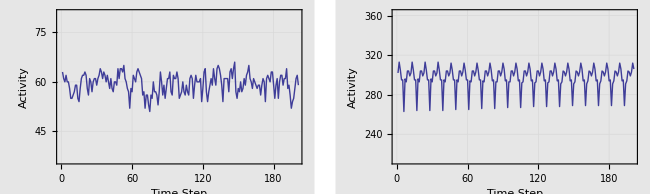

With a high concentration probability, we get very obvious periodicity! The ant colony activity changes in a very consistent way, meaning that the changes in activity are no longer random-- they are, in fact, organized. By putting lots of ants in the same place, we can see that one portion of their existence, their activity, becomes organized. Because the ants use each other to decide what to do, by putting a lot of ants in one place means that they all follow each other, producing organization and periodicity in their activity.

Now that we have seen how some organization occurs when we make an ant colony very concentrated, we can begin to play around with the different parameters and see how they affect how obviously periodic the activity is and the length of the periods themselves.

### Varying p

First, we can look at varying the concentration probability p. We know that the activity is random at low concentrations and organized at high concentrations, but it would be interesting to determine how these colonies evolve from unorganized to organized with rising p values. By creating a number of graphs with different p values, ranging from low values that will produce unorganized activity to high values that will produce organized activity, we can hopefully see when it is these colonies get organized-- essentially, we're looking for the phase transition

To do this, here is a range of plots with p ranging from 0.2 to 0.95. They are all colonies on 20x20 lattices with s, the activity time clock, set to be 10, r, the probability of an inactive ant spontaneously becoming active, set to 0.15. We'll run this colony out for 250 steps and then drop the first 50 in case there are any odd fluctuations at the beginning

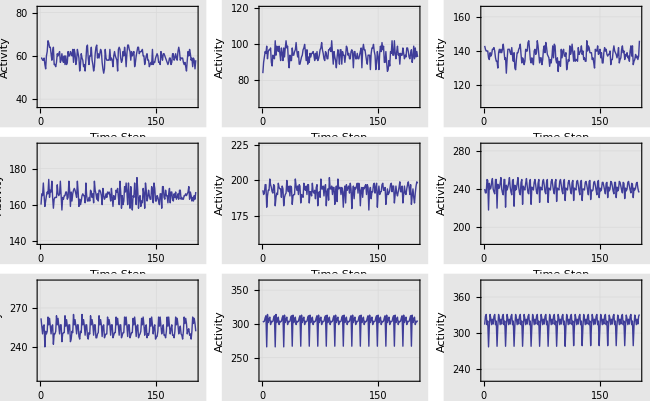

As we can see, the periodicity in the graphs slowly increases when p does. The activity appears pretty random until approximately p=0.6, when we start to see some repeating dips in the activity that look to be evenly spaced out. By the time p=0.7, we cold probably get a reliable number for the period of the activity despite the fact that it's not perfectly periodic (meaning each new cycle is not exactly like the last one). It seems like by p=0.9, we can pretty perfect periodicity, where it doesn't seem like the cycles are any different from each other at all. The transition an unorganized ant colony and an organized one seems to occur somewhere between p=0.6 and p=0.7, but it's tough to determine exactly where the phase transition occurs because we have no harsh definition of what periodicity is. 

This result sheds some light upon the question of how ant colonies maintain any sort of organization at all-- it seems that the answer lies in the density of the ant colonies themselves. If individual ants don't come into contact with other ants very often (corresponded to a small p value), then the activity becomes erratic and random. The ants' ability to go from the inactive to the active state depends only upon its possibility of spontaneously re-activating. On the other hand, if there is a large concentration of ants (corresponding to a large p value), then we see distinctly periodic activity in a colony-- this is because when an ant becomes inactive, it's likely to become active very quickly again because simply by being around other active ants can inactive ants become active again. Thus, if a large group is inactive together, they will likely become active together at the same time as well, resulting in them to having the same activity time clocks, and thus their activity cycles are all aligned. 

We can also see this using an animation. This first animation has p=0.3, which means 3 out of every 10 spots on the lattice are filled by ants.

It doesn't appear to have any sort of obvious periodicity in the animation-- the number of inactive ants, shown in black, seems to remain somewhat constant throughout the course of the animation, with a few fluctuations. 

Now, let's compare that animation to the following one, where p=0.9, so there are very few empty spots remaining on the lattice:

It's tough to see because the simulation runs so quickly, but if you compare the number of inactive ants in the first shot of the animation with the number of inactive ants in the following shots, there is clearly a large portion that starts out inactive. This group, becoming active all together because of the proximity with other active ants, then all becomes inactive again about two-thirds of the way through the simulation, where there is a flash of a large number of ants becoming black (inactive) again. Thus, we can see the physical representation of this periodicity.

### Varying s

Now, let's see what happens when we vary the activity time clock parameter, denoted by s.

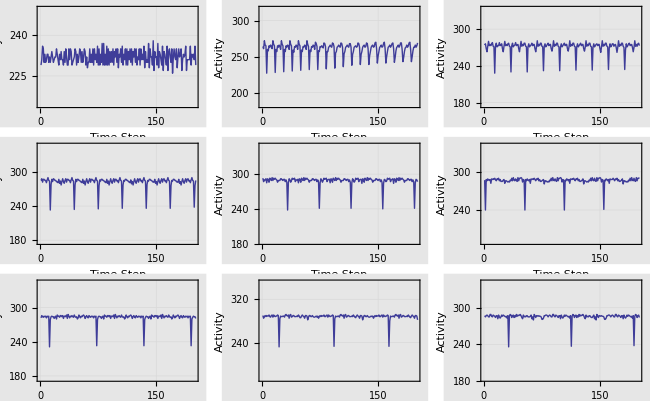

It's clear that changing the value for s, which is the length of the activity clock for any ant, has some dramatic effects on ant colony activity. As the value for s increases higher and higher, the ant colony activity does two things. First, it becomes less "interesting" and becomes more of a combination of flat lines and sharp dips. Second, the period of this activity becomes larger and larger, making the time in-between these dips bigger and bigger. So it seems like the higher the s value, the more the ants become inactive and active in unison. 

These results make sense in light of our model, though-- since ants are randomly chosen to be either active or inactive at the beginning of the simulation, the group of ants that start out inactive become active right away because of how concentrated the ant colony is. This means that all of these ants start with the same time clock, which then eventually runs out at the same time and they are all inactive again for a single time step. The periods of these dips are related to s in a very linear way since the dips in activity are from that initial group becoming inactive again, and this happens every s time steps because that's when they're time clocks run out. 

We can see this in the following plot comparing the period of these dips and the value for s.

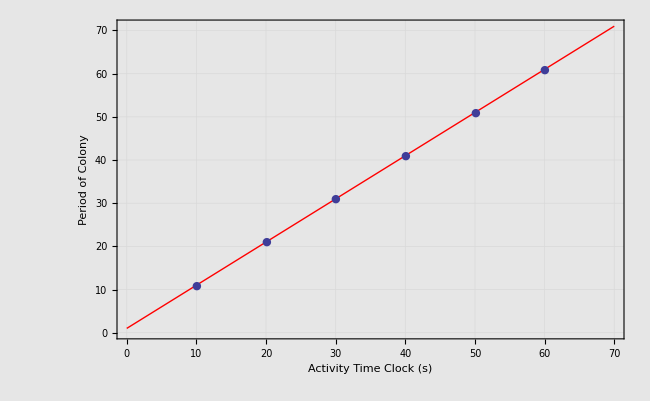

Clearly the relationship between the activity time clock and the period of the colony activity is distinctly linear! This confirms our hypothesis that the dips in the activity are due to a single group that started out inactive together, became active together and were in sync from then on out.

Just to prove that all of this has to do with the concentration probability p, these two plots show that no matter how high we make the s value for an ant colony, the periodicity of the colony simply can't exist if there are too few ants in the colony.

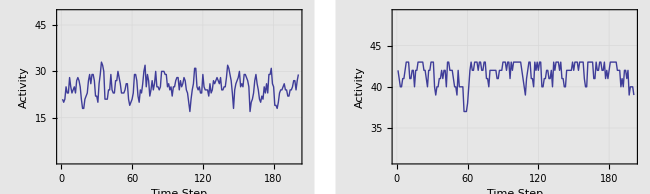

As we can see, there is no apparent periodicity in either of the plots, even though one has a small s value and one has a large s value. Clearly the periodic nature of the colony is reliant upon a large concentration value to produce organization!

## Second Model Results

Now, let's play around with the rules a little bit to see if we can still get periodicity with some different laws governing the ant's activity. In the first model, we set the activity clock of every ant to be a certain number that was the same for every ant. It was this consistency in the activity time clock that created the periodicity that we saw in the activity. Now, however, we'll choose the activity time clock for each ant from a probability distribution. The mean of the distribution will be the inputted s number, given by the user, and the standard deviation will be s/5. This way, not every ant will have the same s value-- in fact, there will be a whole range of possible s values for ants.

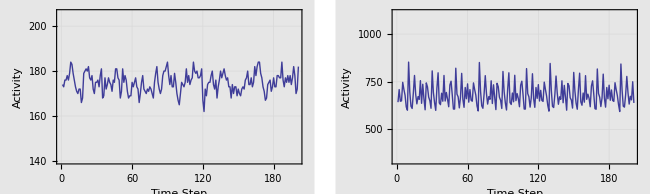

As these two plots show, we clearly can still get some periodicity in the ant colony activity! The first graph, with a low p value and standard values for s and r show the kind of disorganization that we saw in our first model. However, in the second graph, we can clearly get some sort of periodicity! It is not as well defined as it was for our first model, but there is definitely a rhythm to it and some repeating spikes in activity. Another important difference with this second model is the fact that the periodicity doesn't occur under a wide range of parameters, like it did for our first model. In the first model, the as long as we had a large p value, we were able to see some periodicity. In this model, however, if we have a really large value for s, the range of possible values for s for a given ant is too large to make any kind of periodicity. Having an s value of 3, like it is in the two graphs above, still produces a range of possible values for each ant, but the range is small enough that periodicity still occurs.

### Varying p

Now, let's see what happens when we keep all the parameters constant except for the p value to see if we get an increase in periodicity with rising p values, like we did for the last model. To do this, we'll make a range of plots with p values ranging from p=0.1 to p=0.9:

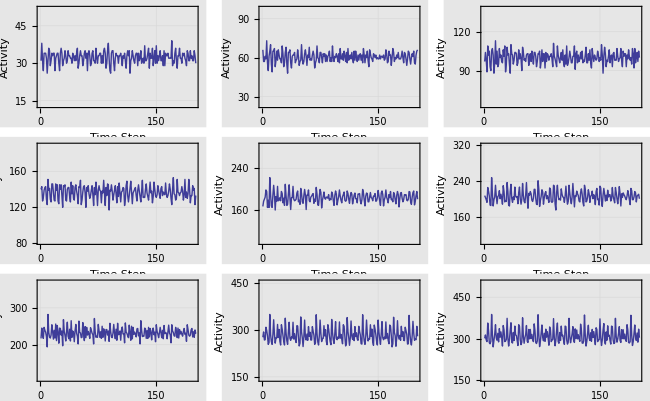

With an increasing p value, we definitely do get an increase in the periodicity of the activity! The periodic nature of the activity is not as distinct as it was in our first model, because of the distribution of s values for each individual ant, but there is an obvious progression from randomness to organization. As it was in our first model, it seems like the activity is random until approximately p=0.6, when we start to see some repeating "bunches" of colony activity. By the time p=0.8, we get pretty regular fluctuations in the activity and it's clearly periodic.

### Varying r

Now, let's see what happens when we play with the r parameter. As I said before, it seems as though the periodicity only occurs under a more restricted set of parameters. This is definitely true for the s values, but let's play around with different values for r, the probability that an inactive ant spontaneously becomes active again. We'll use a range of r values from r=0.15 to r=0.95:

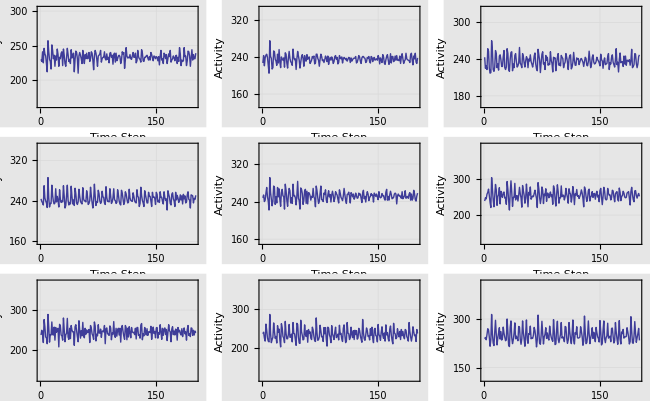

Just like with rising p values, we get more periodicity with larger r values! Again, the periodicity isn't as clear as it was in the first model, but there is a clear evolution from random to organized in these plots. The periodicity first seems to appear around the r=0.75 plot, but the activity seems to trail off and become more random the longer the simulation runs. However, by the r=0.85 plot, the periodicity seems to occur throughout the whole simulation, despite it not being too clear. But by r=0.95, the periodicity is clear and it lasts throughout the whole simulation, giving us the organized ant colony activity that we were looking for.

This result makes a lot of intuitive sense, too-- the more likely ants are to become spontaneously active again, the sooner they'll become active. If the probability is really high, like around p=0.95, then most ants will become active after only being inactive for a single time step-- this makes for organization within the colony because the same dips and spikes will occur as the same ants become inactive and then active again.

### Animations

We can animate our new model just as we did our old one, with the function ListAnimate that will show our ants moving over each time step. Again, the active ants are shown in blue and the inactive are shown in black

The animation looks very similar to the ones from our first model except we can notice a few key differences. First, more of the ants are inactive in this animation and this number stays relatively constant throughout the animation. This is due to the smaller s value, which makes the ants cycling more often through the inactive and active stages-- there are no long periods of very few ants inactive because the time clock is so short. The second thing we can notice is that the ant farm seems to maintain most of its general shape throughout the animation-- many of the unoccupied spaces stay, for the most part, pretty unoccupied. This is because the ants can't stay active long enough to move far around the grid.

## Conclusions

In conclusion, the complex structure of ant colonies is not due to any sort of powerful central control of ants nor to the immense intellect of an individual ant; instead, the organization that occurs in ant colonies results from the fact that there are a lot of ants in a given ant colony. By using a few simple rules programmed into the ants themselves, ants are able to use their interactions with their neighbors to determine what it is they should be doing. In our models, we monitored the ant colony activity, which measured how many ants in the colony were in an "active" state for a given time step. Because an ants activity was partially determined by what its neighbors were doing, colonies with a high density of ants produced colony activity that was distinctly periodic. Colonies that had low concentrations of ants, in contrast, had no periodicity despite the other conditions on the ant colony. We also found periodicity for two different models: one of them set a constant value for the activity time clock, denoted by s, and one of them chose a different s value for each ant based upon a normal probability distribution. Both of these models, however, produced periodicity for certain parameters. This shows that even different models produce this periodicity provided that these models give ants rules for interacting with their neighbors. 

Although our model may only study a simple type of organization in an ant colony, the principles help explain other kinds of organization within ant colonies. Real harvester ants are often split into four different categories: foragers, nest maintenance workers, midden workers, and patrolling ants. In these real colonies, if there is a need for more of a certain worker (like if a large source of food is found), then workers are transferred over from one group to the next to accommodate this new external factor. The ants' ability to do this stems from the same reason why our ant colony activity was periodic with high concentration probability values: simple rules among concentrated groups of individuals can produce complex systems^2. 

These findings, that "swarm intelligence" is really a very powerful thing, can have drastic influences on our daily lives. Dr. Dough Lawson, the analyst at Southwest Airlines, used these properties to develop an algorithm that loads people onto airplanes faster than the standard model. Dr. Lawson treated human beings at an airport like ants-- individuals with simple rules about where they would like to sit on the airplane. Dr. Lawson then used these simple rules to make a complex but efficient system^4. This leaves one wondering, on what other kinds of systems could we apply this model? The world is full of immense systems of individual pieces, and if we can understand how to quantify the rules of these individual pieces, perhaps we can use what we've learned about "swarm intelligence" to create more efficient systems!

## Appendix A: First Model

### Code Setup

Here we can set up the initial skeleton for an ant colony. All of this code was adapted from the code from the book titled "Modeling Nature" by Gaylord and Nishidate.

Here are the different possibilities for a given spot in the lattice:

b -- a border site
0 -- an empty site
-1 -- a site occupied by an inactive ant
1 -- a site occupied by a north-facing ant
2 -- a site occupied by an east-facing ant
3 -- a site occupied by a south-facing ant
4 -- a site occupied by a west-facing ant
A site consist of the ordered pair {x,y} where the first value is one from the list above, and the second number is the activity time clock, which for an active ant is from 1 to s, and for an inactive ant, a border spot, or an empty spot has a value of 0 for this.

And here are the rules for updating the lattice sites in the system:

1. An active ant moves to an adjacent empty site it faces, unless the move will result in a collision with another active ant
2. An active ant facing an adjacent site that is either on the border or is occupied by another ant stays put
3. Ant active ant, whether it moves or not, randomly picks a direction to face in each time step and increments its "activity time clock" (which keeps track of how many time steps have elapsed since the ant became active) by 1. 
4. An active ant becomes inactive after s time steps.
5. An inactive ant becomes active either spontaneously or when an active ant is on an adjacent site.

```mathematica
{s, n, p} = {5, 20, 0.3};
antPopulation =
  Table[{{-1, 1, 2, 3, 4}[[Random[Integer, {1, 5}] ]],
      	Random[Integer, {1, s}]}*Floor[Random[] + p],
    			{n - 1}, {n - 1}] /. {-1, _} -> {-1, 0};
```

Here we set n, which is the size of the lattice, s, which is the activity time clock, and p, which is the probability that ants are placed in the lattice. This code creates the basics of the lattice

```mathematica
Clear[border,b]
border[population_]=Append[Map[Append[#,{b,0}]&,#],Table[{b,0},{Length[#]+1}]]&;
```

Now we set up the borders for the ant farm to make the lattice complete

```mathematica
antFarm=border[antPopulation];
```

Now we need to set up the ant density:

```mathematica
antDensity=N[Apply[Plus,
	Abs[Sign[Transpose[Flatten[antPopulation,1]]]]]/n^2];
```

#### Statistical Functions

```mathematica
Clear[ave,aveSqr,var,unc]
ave[myList_]:=N[Apply[Plus,myList]/Length[myList]];
aveSqr[myList_]:=N[Apply[Plus,myList^2]/Length[myList]];
var[myList_]:=aveSqr[myList]-ave[myList]^2;
unc[myList_]:=Sqrt[var[myList]/Length[myList]];
```

Here are some statistical functions that we might need. These were taken from the notebooks of Bill Titus.

### Code Development

The rules for the behavior of an ant during a time steps looks something like this:

```mathematica
ant[site,N,E,S,W,NE,SE,SW,NW,Nn,Ee,Ss,Ww]
```

ant[site,N,ⅇ,S,W,NE,SE,SW,NW,Nn,Ee,Ss,Ww]

where the arguments represent the value of the site and the 12 nearest neighbors: the nearest neighbors in the N, E, S, W directions, the nearest neighbors in the NE, SE, SW, NW directions, and the next nearest neighbors in the N, E, S, W directions. 

We can then use the random number generator function by Mathematica to determine the direction that an ant faces:

```mathematica
RND:=Random[Integer,{1,4}]
```

#### Inactive ant adjacent to an active ant:

```mathematica
ant[{-1,0},{x_?Positive,_},_,_,_,_,_,_,_,_,_,_,_]:={RND,1}
ant[{-1,0},_,{x_?Positive,_},_,_,_,_,_,_,_,_,_,_]:={RND,1}
ant[{-1,0},_,_,{x_?Positive,_},_,_,_,_,_,_,_,_,_]:={RND,1}
ant[{-1,0},_,_,_,{x_?Positive,_},_,_,_,_,_,_,_,_]:={RND,1}
```

This sets the ant to have a random direction to face and an activity clock of 1

#### Inactive ant randomly becoming active

```mathematica
ant[{-1,0},_,_,_,_,_,_,_,_,_,_,_,_]:=
		{ -1+# * Random[Integer,{2,5}],#}&[Floor[Random[]+r]]
```

The ant becomes active with a probability of r and it randomly chooses a direction to face and sets its activity clock back to 1.

#### Active Ants becoming inactive

```mathematica
ant[{x_?Positive,s},_,_,_,_,_,_,_,_,_,_,_,_]:={-1,0}
```

This just sets an active ant to become inactive if its activity clock has gone to s

#### Active ants facing an adjacent site that's either on the border or has another ant

```mathematica
ant[{1,y_},{-1|x_?Positive|b,_},_,_,_,_,_,_,_,_,_,_,_]:={RND,y+1}
ant[{2,y_},_,{-1|x_?Positive|b,_},_,_,_,_,_,_,_,_,_,_]:={RND,y+1}
ant[{3,y_},_,_,{-1|x_?Positive|b,_},_,_,_,_,_,_,_,_,_]:={RND,y+1}
ant[{4,y_},_,_,_,{-1|x_?Positive|b,_},_,_,_,_,_,_,_,_]:={RND,y+1}
```

These ants stay put, randomly choose a new direction to face, and increment the activity clock by 1

#### Active ant facing an empty adjacent site that is also faced by another active ant

```mathematica
ant[{1,y_},{0,0},_,_,_,{4,_},_,_,_,_,_,_,_]:={RND,y+1}
ant[{1,y_},{0,0},_,_,_,_,_,_,{2,_},_,_,_,_]:={RND,y+1}
ant[{1,y_},{0,0},_,_,_,_,_,_,_,{3,_},_,_,_]:={RND,y+1}
ant[{2,y_},_,{0,0},_,_,{3,_},_,_,_,_,_,_,_]:={RND,y+1}
ant[{2,y_},_,{0,0},_,_,_,{1,_},_,_,_,_,_,_]:={RND,y+1}
ant[{2,y_},_,{0,0},_,_,_,_,_,_,_,{4,_},_,_]:={RND,y+1}
ant[{3,y_},_,_,{0,0},_,_,{4,_},_,_,_,_,_,_]:={RND,y+1}
ant[{3,y_},_,_,{0,0},_,_,_,{2,_},_,_,_,_,_]:={RND,y+1}
ant[{3,y_},_,_,{0,0},_,_,_,_,_,_,_,{1,_},_]:={RND,y+1}
ant[{4,y_},_,_,_,{0,0},_,_,{1,_},_,_,_,_,_]:={RND,y+1}
ant[{4,y_},_,_,_,{0,0},_,_,_,{3,_},_,_,_,_]:={RND,y+1}
ant[{4,y_},_,_,_,{0,0},_,_,_,_,_,_,_,{2,_}]:={RND,y+1}
```

These ants stay put, randomly choose a new direction to face, and increment their activity clocks by 1

#### Active ants facing an empty adjacent site

```mathematica
ant[{1,_},{0,0},_,_,_,_,_,_,_,_,_,_,_]:={0,0}
ant[{2,_},_,{0,0},_,_,_,_,_,_,_,_,_,_]:={0,0}
ant[{3,_},_,_,{0,0},_,_,_,_,_,_,_,_,_]:={0,0}
ant[{4,_},_,_,_,{0,0},_,_,_,_,_,_,_,_]:={0,0}
```

These ants simply vacates the site that they were on and they move!

#### Empty site faced by two or more active ants

```mathematica
ant[{0,0},{3,_},{4,_},_,_,_,_,_,_,_,_,_,_]:={0,0}
ant[{0,0},{3,_},_,{1,_},_,_,_,_,_,_,_,_,_]:={0,0}
ant[{0,0},{3,_},_,_,{2,_},_,_,_,_,_,_,_,_]:={0,0}
ant[{0,0},_,{4,_},{1,_},_,_,_,_,_,_,_,_,_]:={0,0}
ant[{0,0},_,{4,_},_,{2,_},_,_,_,_,_,_,_,_]:={0,0}
ant[{0,0},_,_,{1,_},{2,_},_,_,_,_,_,_,_,_]:={0,0}
```

These empty sites just stay empty

#### Empty site faced by one active ant that has been active for less than s time steps

```mathematica
ant[{0,0},{3,y_?(#<s&)},_,_,_,_,_,_,_,_,_,_,_]:={RND,y+1}
ant[{0,0},_,{4,y_?(#<s&)},_,_,_,_,_,_,_,_,_,_]:={RND,y+1}
ant[{0,0},_,_,{1,y_?(#<s&)},_,_,_,_,_,_,_,_,_]:={RND,y+1}
ant[{0,0},_,_,_,{2,y_?(#<s&)},_,_,_,_,_,_,_,_]:={RND,y+1}
```

These sites become occupied by the ant and the ant then randomly chooses a direction to face and increments its activity clock by 1

#### Empty sites facing 0 ants

```mathematica
ant[{0,0},_,_,_,_,_,_,_,_,_,_,_,_]:={0,0}
```

Empty sites with no ants facing them stay as they are

Border sites just stay as they are:

```mathematica
ant[{b,0},_,_,_,_,_,_,_,_,_,_,_,_]:={b,0}
```

#### Section 04: Applying the Rules

We can use the following function to apply the ant rules to the 13 arguments representing the site and its neighbors

MvonN[func__, lat_] :=
 MapThread[func, Map[RotateRight[lat, #] &,
   		{{0, 0}, {1, 0}, {0, -1}, {-1, 0}, {0, 1},
    		{1, -1}, {-1, -1}, {-1, 1}, {1, 1},
    		{2, 0}, {0, -2}, {-2, 0}, {0, 2}}], 2]

Where we would use it like

MvonN[ant, #] &

We then can use the NestList function to update the ant farm over t time steps by repeatedly applying the anonymous function update to the ant colony lattice

evolve = NestList[MvonN[ant, #] &, initConf, t]

We can also take off the activity time clock from each site by mapping the anonymous function onto the list given in evolve:

latticeConfig = Function[y, Map[#[[1]] &, y, {2}]]

Map[latticeConfig, evolve]

### Code

```mathematica
samsFarm[n_,p_,s_,r_,t_]:=
Module[{antPopulation,antFarm,border,ant},

antPopulation=
Table[{{-1,1,2,3,4}[[Random[Integer,{1,5}]]],
Random[Integer,{1,s}]}* Floor[Random[]+p],
	{n-1},{n-1}]/.{-1,_}->{-1,0};

border=PadLeft[Append[Map[Append[#,{b,0}]&,#],Table[{b,0},{Length[#]+1}]],{n+1,n+1},{{{b,0}}}]&;

antFarm=border[antPopulation];

RND:=Random[Integer,{1,4}];

ant[{-1,0},{x_?Positive,_},_,_,_,_,_,_,_,_,_,_,_]:={RND,1};
ant[{-1,0},_,{x_?Positive,_},_,_,_,_,_,_,_,_,_,_]:={RND,1};
ant[{-1,0},_,_,{x_?Positive,_},_,_,_,_,_,_,_,_,_]:={RND,1};
ant[{-1,0},_,_,_,{x_?Positive,_},_,_,_,_,_,_,_,_]:={RND,1};

ant[{-1,0},_,_,_,_,_,_,_,_,_,_,_,_]:=
		{ -1+# * Random[Integer,{2,5}],#}&[Floor[Random[]+r]];

ant[{x_?Positive,s},_,_,_,_,_,_,_,_,_,_,_,_]:={-1,0};


ant[{1,y_},{-1|x_?Positive|b,_},_,_,_,_,_,_,_,_,_,_,_]:={RND,y+1};
ant[{2,y_},_,{-1|x_?Positive|b,_},_,_,_,_,_,_,_,_,_,_]:={RND,y+1};
ant[{3,y_},_,_,{-1|x_?Positive|b,_},_,_,_,_,_,_,_,_,_]:={RND,y+1};
ant[{4,y_},_,_,_,{-1|x_?Positive|b,_},_,_,_,_,_,_,_,_]:={RND,y+1};

 ant[{1,y_},{0,0},_,_,_,{4,_},_,_,_,_,_,_,_]:={RND,y+1};
ant[{1,y_},{0,0},_,_,_,_,_,_,{2,_},_,_,_,_]:={RND,y+1};
ant[{1,y_},{0,0},_,_,_,_,_,_,_,{3,_},_,_,_]:={RND,y+1};
ant[{2,y_},_,{0,0},_,_,{3,_},_,_,_,_,_,_,_]:={RND,y+1};
ant[{2,y_},_,{0,0},_,_,_,{1,_},_,_,_,_,_,_]:={RND,y+1};
ant[{2,y_},_,{0,0},_,_,_,_,_,_,_,{4,_},_,_]:={RND,y+1};
ant[{3,y_},_,_,{0,0},_,_,{4,_},_,_,_,_,_,_]:={RND,y+1};
ant[{3,y_},_,_,{0,0},_,_,_,{2,_},_,_,_,_,_]:={RND,y+1};
ant[{3,y_},_,_,{0,0},_,_,_,_,_,_,_,{1,_},_]:={RND,y+1};
ant[{4,y_},_,_,_,{0,0},_,_,{1,_},_,_,_,_,_]:={RND,y+1};
ant[{4,y_},_,_,_,{0,0},_,_,_,{3,_},_,_,_,_]:={RND,y+1};
ant[{4,y_},_,_,_,{0,0},_,_,_,_,_,_,_,{2,_}]:={RND,y+1};

ant[{1,_},{0,0},_,_,_,_,_,_,_,_,_,_,_]:={0,0};
ant[{2,_},_,{0,0},_,_,_,_,_,_,_,_,_,_]:={0,0};
ant[{3,_},_,_,{0,0},_,_,_,_,_,_,_,_,_]:={0,0};
ant[{4,_},_,_,_,{0,0},_,_,_,_,_,_,_,_]:={0,0};

ant[{0,0},{3,_},{4,_},_,_,_,_,_,_,_,_,_,_]:={0,0};
ant[{0,0},{3,_},_,{1,_},_,_,_,_,_,_,_,_,_]:={0,0};
ant[{0,0},{3,_},_,_,{2,_},_,_,_,_,_,_,_,_]:={0,0};
ant[{0,0},_,{4,_},{1,_},_,_,_,_,_,_,_,_,_]:={0,0};
ant[{0,0},_,{4,_},_,{2,_},_,_,_,_,_,_,_,_]:={0,0};
ant[{0,0},_,_,{1,_},{2,_},_,_,_,_,_,_,_,_]:={0,0};

ant[{0,0},{3,y_?(#<s&)},_,_,_,_,_,_,_,_,_,_,_]:={RND,y+1};
ant[{0,0},_,{4,y_?(#<s&)},_,_,_,_,_,_,_,_,_,_]:={RND,y+1};
ant[{0,0},_,_,{1,y_?(#<s&)},_,_,_,_,_,_,_,_,_]:={RND,y+1};
ant[{0,0},_,_,_,{2,y_?(#<s&)},_,_,_,_,_,_,_,_]:={RND,y+1};

ant[{0,0},_,_,_,_,_,_,_,_,_,_,_,_]:={0,0};
ant[{b,0},_,_,_,_,_,_,_,_,_,_,_,_]:={b,0};

MvonN[func__,lat_]:=
MapThread[func,Map[RotateRight[lat,#]&,
		{{0,0},{1,0},{0,-1},{-1,0},{0,1},
		{1,-1},{-1,-1},{-1,1},{1,1},
		{2,0},{0,-2},{-2,0},{0,2}}],2];

NestList[MvonN[ant,#]&,antFarm,t]
]
```

### Code Test

```mathematica
samsFarm[5,0.8,10,0.15,3]//MatrixForm
```

((b | 0
b | 0
b | 0
b | 0
b | 0
b | 0) | (b | 0
2 | 6
0 | 0
4 | 5
2 | 1
b | 0) | (b | 0
4 | 2
1 | 5
-1 | 0
0 | 0
b | 0) | (b | 0
4 | 5
0 | 0
-1 | 0
-1 | 0
b | 0) | (b | 0
-1 | 0
2 | 4
0 | 0
2 | 7
b | 0) | (b | 0
b | 0
b | 0
b | 0
b | 0
b | 0)
(b | 0
b | 0
b | 0
b | 0
b | 0
b | 0) | (b | 0
3 | 7
0 | 0
3 | 6
1 | 2
b | 0) | (b | 0
1 | 3
1 | 6
1 | 1
0 | 0
b | 0) | (b | 0
2 | 6
0 | 0
-1 | 0
4 | 1
b | 0) | (b | 0
3 | 1
0 | 0
1 | 5
1 | 8
b | 0) | (b | 0
b | 0
b | 0
b | 0
b | 0
b | 0)
(b | 0
b | 0
b | 0
b | 0
b | 0
b | 0) | (b | 0
4 | 8
2 | 7
3 | 7
3 | 3
b | 0) | (b | 0
4 | 4
0 | 0
2 | 2
0 | 0
b | 0) | (b | 0
0 | 0
2 | 7
4 | 1
1 | 2
b | 0) | (b | 0
2 | 2
0 | 0
1 | 6
2 | 9
b | 0) | (b | 0
b | 0
b | 0
b | 0
b | 0
b | 0)
(b | 0
b | 0
b | 0
b | 0
b | 0
b | 0) | (b | 0
3 | 9
1 | 8
1 | 8
2 | 4
b | 0) | (b | 0
2 | 5
0 | 0
4 | 3
0 | 0
b | 0) | (b | 0
0 | 0
1 | 8
3 | 2
1 | 3
b | 0) | (b | 0
0 | 0
1 | 3
3 | 7
4 | 10
b | 0) | (b | 0
b | 0
b | 0
b | 0
b | 0
b | 0))

Looks pretty good to me! If you follow individual ants, you can see how they move throughout the lattice and you can see their time clocks changing!

## Appendix B: Results of First Model

We can think about the activity of the ant colony as a function of time by plotting the number of active ants as a function of time. 

We can do that with the following code:

### Code

```mathematica
plotFunction[n_,p_,s_,r_,t_,tMin_]:=
Module[
{farm,plot, min, max, range},

SeedRandom[];
farm=Map[Count[Flatten[#,1],{x_?Positive,_}]&,
Drop[samsFarm[n,p,s,r,t],tMin]];

min=Min[farm[[1;;t-tMin]]];
max=Max[farm[[1;;t-tMin]]];
range=max-min;

ListPlot[farm,
		PlotRange->{{0,t-tMin},{min-range,max+range}},
		Frame->True,
		PlotJoined->True,
		PlotStyle->Thick,
		FrameLabel->{"Time Step","Activity",StringForm["Ant Colony Activity: p = ``, s = ``, r = ``",p, s, r],""},
		GridLines->Automatic,
		ImageSize->500,
		Background->GrayLevel[0.9]]

];
```

### Code Runs

Now, let's use the plot function to display ant colony activity for two different p values--for p=0.2 and for p=0.9

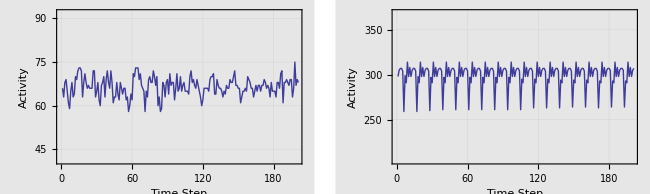

```mathematica
plot01=plotFunction[20,0.2,10,0.15,250,50];
plot02=plotFunction[20,0.9,10,0.15,250,50];
GraphicsGrid[{{plot01,plot02}},ImageSize->650]
```

As we can see, there is no discernible periodicity in the plot with p=0.2 but the periodicity is quite clear when p=0.9. Clearly, with an increase in the probability of ants being in a given lattice spot, we get a much more organized, controlled ant colony. This explains why ants on their own are fairly erratic and unintelligent; as a group, however, they can be organized and can accomplish amazing things!

#### Varying p

Let's make a large number of plots with different p values so that we can see exactly when the transition is between a lack of organization and periodicity.

```mathematica
plot01p=plotFunction[20,0.45,10,0.15,250,50];
plot02p=plotFunction[20,0.5,10,0.15,250,50];
plot03p=plotFunction[20,0.55,10,0.15,250,50];
plot04p=plotFunction[20,0.6,10,0.15,250,50];
plot05p=plotFunction[20,0.65,10,0.15,250,50];
plot06p=plotFunction[20,0.7,10,0.15,250,50];
plot07p=plotFunction[20,0.75,10,0.15,250,50];
plot08p=plotFunction[20,0.8,10,0.15,250,50];
plot09p=plotFunction[20,0.85,10,0.15,250,50];
plotListP={plot01p,plot02p,plot03p,plot04p,plot05p,plot06p,plot07p,plot08p,plot09p};
```

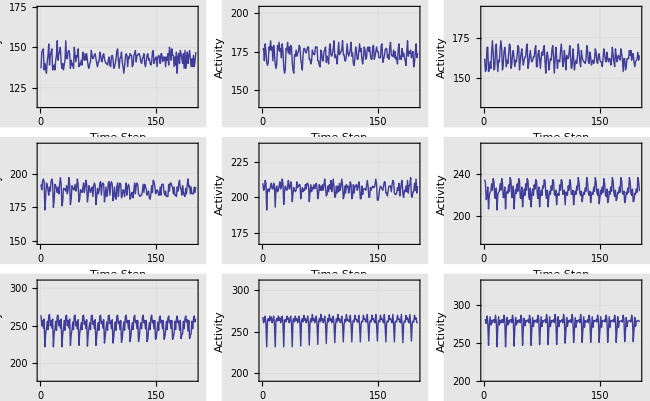

```mathematica
GraphicsGrid[Partition[plotListP,3],ImageSize->650]
```

As we can see, the periodicity in the graphs increases with an increase in p. The activity appears pretty random until approximately p=0.45. By the time p=0.55, we can pretty reliably measure the period for the ant colony activity, and by the plots with p=0.75 and p=0.8, we could easily measure the period on the ant colony activity. It's tough to define where exactly this phase transition occurs, from organization to disorganization-- I can't figure out a good way to determine this. 

Power spectrum, Fourier analysis

#### Varying s

Now, let's look at what happens when we vary the s parameter for a wide range of ant colonies, all with the same p value.

```mathematica
plot01s=plotFunction[20,0.8,5,0.15,250,50];
plot02s=plotFunction[20,0.8,10,0.15,250,50];
plot03s=plotFunction[20,0.8,20,0.15,250,50];
plot04s=plotFunction[20,0.8,30,0.15,250,50];
plot05s=plotFunction[20,0.8,40,0.15,250,50];
plot06s=plotFunction[20,0.8,50,0.15,250,50];
plot07s=plotFunction[20,0.8,60,0.15,250,50];
plot08s=plotFunction[20,0.8,70,0.15,250,50];
plot09s=plotFunction[20,0.8,80,0.15,250,50];
plotListS={plot01s,plot02s,plot03s,plot04s,plot05s,plot06s,plot07s,plot08s,plot09s};
```

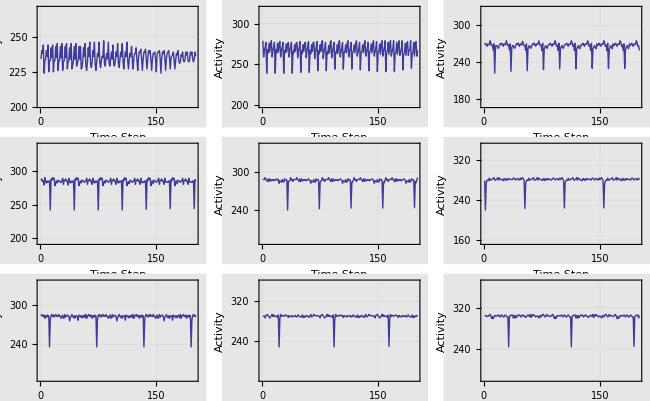

```mathematica
GraphicsGrid[Partition[plotListS,3],ImageSize->650]
```

It's clear that changing the value for s, which is the lengthLent of the activity clock for any ant, has some dramatic effects on ant colony activity. As the value for s increases higher and higher, the ant colony activity does two things. First, it becomes less "interesting" and becomes more of a combination of flat lines and sharp dips. The dips also seem to get deeper but then they seem to stop their increasing depth... the line seems to get closer and closer to 250 and the dips drop to almost exactly 200. The reason for this increase in size of the dip

Second, the period of this activity becomes larger and larger, making the time in-between these dips bigger and bigger. So it seems like the higher the s value, the more the ants become inactive and active in unison.

However, no matter how big the s value is, the probability has to be large enough to create periodicity-- we can see this in the plots below, where there is no periodicity even when s=80.

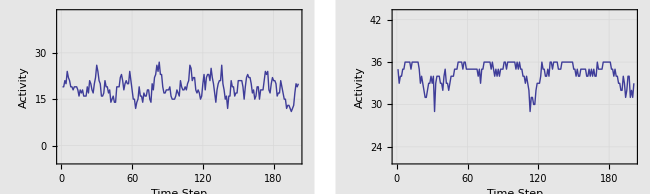

```mathematica
plot10s=plotFunction[20,0.1,5,0.15,250,50];
plot11s=plotFunction[20,0.1,80,0.15,250,50];
GraphicsGrid[{{plot10s,plot11s}},ImageSize->650]
```

#### Varying r

Now, let's see what happens when we change r, which is the probability that an inactive ant spontaneously becomes active again.

```mathematica
plot01r=plotFunction[20,0.7,10,0.15,250,50];
plot02r=plotFunction[20,0.7,10,0.25,250,50];
plot03r=plotFunction[20,0.7,10,0.35,250,50];
plot04r=plotFunction[20,0.7,10,0.45,250,50];
plot05r=plotFunction[20,0.7,10,0.55,250,50];
plot06r=plotFunction[20,0.7,10,0.65,250,50];
plot07r=plotFunction[20,0.7,10,0.75,250,50];
plot08r=plotFunction[20,0.7,10,0.85,250,50];
plot09r=plotFunction[20,0.7,10,0.95,250,50];
plotListR={plot01r,plot02r,plot03r,plot04r,plot05r,plot06r,plot07r,plot08r,plot09r};
```

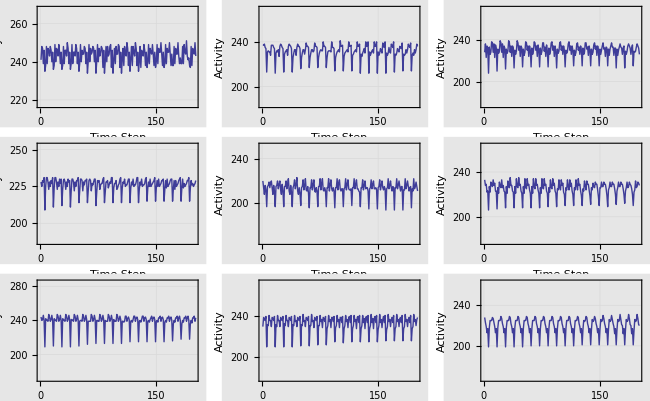

```mathematica
GraphicsGrid[Partition[plotListR,3],ImageSize->650]
```

It seems that r is a parameter that doesn't have much of an effect on the periodicity of the colony activity. It's possibly looks like the activity becomes more regular with an increase in r, but the change is not terribly noticeable.

#### Varying n

Now let's see what happens when we keep everything constant except for the lattice size.

```mathematica
plot01n=plotFunction[10,0.7,10,0.15,250,50];
plot02n=plotFunction[20,0.7,10,0.15,250,50];
plot03n=plotFunction[30,0.7,10,0.15,250,50];
plot04n=plotFunction[40,0.7,10,0.15,250,50];
plot05n=plotFunction[50,0.7,10,0.15,250,50];
plot06n=plotFunction[60,0.7,10,0.15,250,50];
plot07n=plotFunction[70,0.7,10,0.15,250,50];
plot08n=plotFunction[80,0.7,10,0.15,250,50];
plot09n=plotFunction[90,0.7,10,0.15,250,50];
plotListN={plot01n,plot02n,plot03n,plot04n,plot05n,plot06n,plot07n,plot08n,plot09n};
```

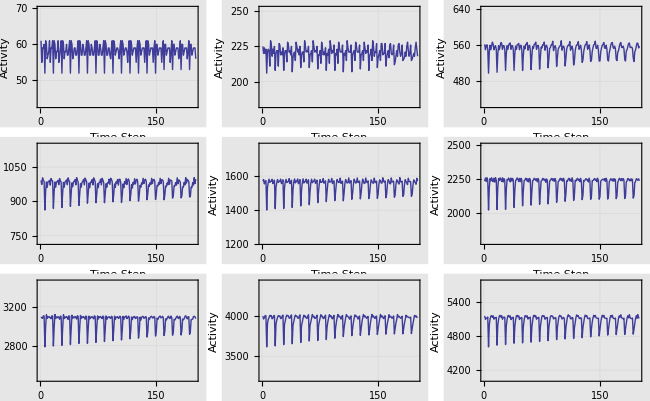

```mathematica
GraphicsGrid[Partition[plotListN,3],ImageSize->650]
```

Changing the value for n doesn't seem to do much for the plot... it seem that for a small n value, like n=10, it could have an effect on the periodicity since there just aren't enough ants to make the activity periodic, but once the n value gets to 20, we get pretty regular periodicity in the activity, so varying the n parameter doesn't seem to do much for us.

## Appendix C: Period as a Function of s

Here we're trying to find the relationship between the period of the activity of ant colony versus the time activity clock, denoted by the symbol s

### Setting up Stuff

```mathematica
periodList={};
```

### s=10

```mathematica
s=10;
newFarm1=samsFarm[20,0.8,s,0.15,250];
activity1=Map[Count[Flatten[#,1],{x_?Positive,_}]&,
Drop[newFarm1,100]]
```

{262,260,268,267,268,265,261,260,265,264,238,262,260,269,267,268,265,261,261,265,264,238,262,260,269,266,268,265,261,261,265,263,238,262,260,270,266,268,265,261,261,266,263,237,261,260,269,266,268,265,261,261,265,264,238,260,261,269,266,268,265,261,262,265,264,239,260,261,268,266,268,265,261,262,264,264,239,260,262,268,266,268,265,261,263,264,264,238,260,262,268,266,268,265,261,263,264,265,238,260,262,268,266,268,265,261,263,264,265,238,260,262,268,266,268,265,261,263,264,265,238,260,262,268,266,268,265,260,263,264,265,237,260,262,268,266,268,266,260,263,264,266,236,260,261,267,266,268,266,260,263}

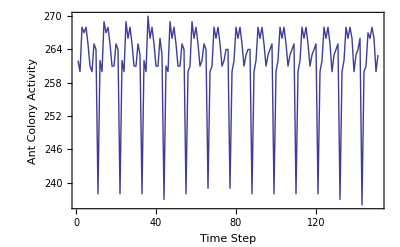

```mathematica
ListPlot[activity1,PlotJoined->True,PlotRange->All,Frame->True,Axes->None,FrameLabel->{"Time Step","Ant Colony Activity",StringForm["Ant Colony Activity with s = ``",s],""}]
```

After looking at the list, it seems like the period is 11

```mathematica
AppendTo[periodList,{s,11}]
```

{{10,11}}

```mathematica
Clear[s]
s=20;
newFarm2=samsFarm[20,0.8,s,0.15,250];
activity2=Map[Count[Flatten[#,1],{x_?Positive,_}]&,
Drop[newFarm2,100]]
```

{271,275,275,271,265,234,266,275,277,274,269,276,275,273,271,271,270,276,271,272,270,270,275,275,271,265,234,265,274,276,275,269,275,275,273,272,271,270,277,271,271,271,270,275,275,271,265,235,266,275,276,275,270,275,275,273,272,271,269,276,272,271,271,270,275,275,271,265,235,264,275,276,275,268,274,275,273,272,272,270,276,272,270,271,270,275,275,271,265,237,264,275,276,277,269,274,275,273,272,272,270,276,273,270,271,270,275,275,271,265,237,263,275,276,277,269,274,275,273,271,272,270,276,273,270,271,270,275,275,269,265,238,263,275,276,277,269,274,275,274,271,272,270,276,273,270,271,270,275,277,269}

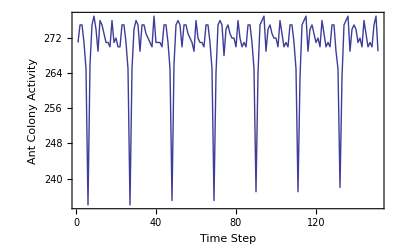

```mathematica
ListPlot[activity2,PlotJoined->True,PlotRange->All,Frame->True,Axes->None,FrameLabel->{"Time Step","Ant Colony Activity",StringForm["Ant Colony Activity with s = ``",s],""}]
```

Looks like the period is 21

```mathematica
AppendTo[periodList,{s,21}]
```

{{10,11},{20,21}}

```mathematica
Clear[s]
s=30;
newFarm3=samsFarm[20,0.8,s,0.15,250];
activity3=Map[Count[Flatten[#,1],{x_?Positive,_}]&,
Drop[newFarm3,100]]
```

{280,280,285,285,281,276,278,279,288,279,286,279,276,281,279,275,279,282,288,280,282,281,281,279,227,268,279,280,282,278,283,279,279,285,285,281,276,278,279,288,279,286,279,276,281,279,275,279,282,288,280,282,281,281,279,231,267,279,280,282,278,284,280,279,285,285,281,276,277,279,288,279,286,279,276,281,279,275,279,282,288,280,282,281,281,279,232,266,279,280,282,278,284,280,279,285,285,281,277,276,278,287,278,286,279,276,281,279,275,279,282,288,280,282,281,281,279,233,265,279,280,282,278,284,280,279,285,285,281,278,277,279,287,278,286,279,276,281,279,275,279,282,288,280,282,281,280,279,234,264,278}

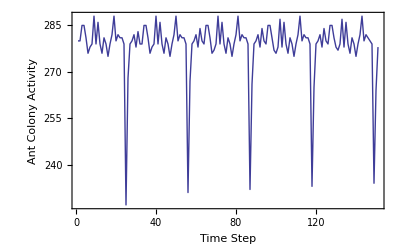

```mathematica
ListPlot[activity3,PlotJoined->True,PlotRange->All,Frame->True,Axes->None,FrameLabel->{"Time Step","Ant Colony Activity",StringForm["Ant Colony Activity with s = ``",s],""}]
```

Looks like the period is 31

```mathematica
AppendTo[periodList,{s,31}]
```

{{10,11},{20,21},{30,31}}

```mathematica
s=40;
newFarm4=samsFarm[20,0.8,s,0.15,250];
activity4=Map[Count[Flatten[#,1],{x_?Positive,_}]&,
Drop[newFarm4,100]]
```

{299,300,295,300,298,300,300,296,298,297,301,297,294,302,298,297,300,292,297,298,303,297,294,243,294,297,297,298,299,298,295,298,297,294,301,299,300,301,298,296,300,299,300,295,301,299,300,300,296,298,297,301,297,294,302,298,297,300,292,297,298,303,297,294,243,294,297,297,298,299,298,295,298,297,294,301,299,300,301,298,296,300,299,300,295,301,299,300,300,296,298,297,301,297,294,302,298,297,300,292,297,298,303,297,294,243,294,297,297,298,299,298,295,298,297,294,301,299,300,301,298,296,300,299,300,295,301,299,300,300,296,298,297,301,297,294,302,298,297,300,292,297,298,303,297,293,243,294,297,297,298}

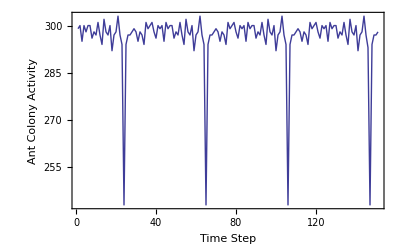

```mathematica
ListPlot[activity4,PlotJoined->True,PlotRange->All,Frame->True,Axes->None,FrameLabel->{"Time Step","Ant Colony Activity",StringForm["Ant Colony Activity with s = ``",s],""}]
```

Looks like the period is 41

```mathematica
AppendTo[periodList,{s,41}]
```

{{10,11},{20,21},{30,31},{40,41}}

```mathematica
s=50;
newFarm5=samsFarm[20,0.8,s,0.15,250];
activity5=Map[Count[Flatten[#,1],{x_?Positive,_}]&,
Drop[newFarm5,100]]
```

{265,266,219,262,265,265,266,267,269,267,264,266,268,267,266,267,267,263,266,266,265,268,268,269,264,262,264,267,267,266,264,264,263,265,266,267,263,264,265,263,263,266,269,265,268,269,265,267,263,266,264,265,266,219,260,265,265,266,267,269,267,264,266,268,267,266,266,266,263,266,266,265,268,268,269,264,262,264,267,267,266,264,264,263,265,266,267,263,264,265,263,263,266,269,265,268,269,265,267,263,266,264,265,266,221,259,265,265,266,267,269,267,264,266,268,267,267,267,266,263,266,266,265,268,268,269,264,262,264,267,267,266,264,264,263,265,266,267,263,264,265,263,263,266,269,265,268,269,265,267,263}

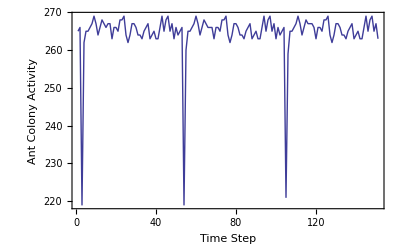

```mathematica
ListPlot[activity5,PlotJoined->True,PlotRange->All,Frame->True,Axes->None,FrameLabel->{"Time Step","Ant Colony Activity",StringForm["Ant Colony Activity with s = ``",s],""}]
```

Looks like the period is 51

```mathematica
AppendTo[periodList,{s,51}]
```

{{10,11},{20,21},{30,31},{40,41},{50,51}}

```mathematica
s=60;
newFarm6=samsFarm[20,0.8,s,0.15,250];
activity6=Map[Count[Flatten[#,1],{x_?Positive,_}]&,
Drop[newFarm6,100]]
```

{286,287,287,288,289,289,284,289,286,290,290,289,289,290,285,284,289,286,288,290,289,287,231,286,290,288,289,288,291,290,291,287,286,288,288,288,289,285,288,290,288,289,288,290,291,290,286,289,290,290,288,292,291,285,284,290,288,290,287,285,285,286,287,287,287,289,289,284,289,286,290,290,289,289,290,285,284,289,286,288,290,289,287,231,286,290,288,289,288,291,290,291,287,286,288,288,288,289,285,288,290,288,289,288,290,291,290,286,289,290,290,288,292,291,285,284,290,288,290,287,285,285,286,287,288,287,289,289,284,289,286,290,290,289,289,290,285,284,289,286,288,290,289,287,231,285,290,288,289,288,291}

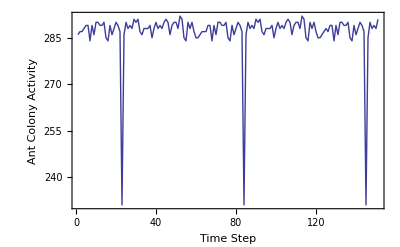

```mathematica
ListPlot[activity6,PlotJoined->True,PlotRange->All,Frame->True,Axes->None,FrameLabel->{"Time Step","Ant Colony Activity",StringForm["Ant Colony Activity with s = ``",s],""}]
```

Looks like the period is 61

```mathematica
AppendTo[periodList,{s,61}]
```

{{10,11},{20,21},{30,31},{40,41},{50,51},{60,61}}

### Fitting and Plotting

Now, let's fit a line to this data to see how linear it is

```mathematica
fit[x_]=Fit[periodList,{1,x},x]
```

1.+1. x

Looks like the fit function produced a pretty basic line with a slope of 1... so our data is clearly linear! Let's plot the data and the line over it just to make sure

```mathematica
linePlot=Plot[fit[x],{x,0,70},Frame->True,GridLines->Automatic,FrameLabel->{"Activity Time Clock (s)","Period of Colony", "Period of Colony as a Function of Activity Time Clock",""},PlotStyle->{Thick,Red},ImageSize->650,Background->GrayLevel[0.9]];
```

```mathematica
sPlot=ListPlot[periodList,Frame->True,GridLines->Automatic,FrameLabel->{"Activity Time Clock (s)","Period of Colony", "Period of Colony as a Function of Activity Time Clock",""},PlotMarkers->{Automatic,Medium},ImageSize->650,Background->GrayLevel[0.9]];
```

```mathematica
Show[linePlot,sPlot]
```

-Graphics-

## Appendix D: Animating a Colony

Here, we would like to be able to see the ants moving around in their spots in the lattice so that we can make sure that our model is actually working... to do that, we'll represent ants with squares and show their movement using the Graphics function.

### Code Development

We want to make a background rectangle that will encompass the whole colony, so let's play around with the Rectangle function within Graphics

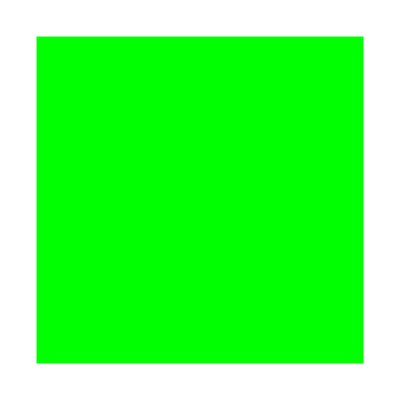

```mathematica
background=Graphics[{Green,Rectangle[{0,0},{5,5}]}]
```

Now we want to be able to add little dots to this one that represent ants, so let's add an ant at the position {2,3}:

```mathematica
antSquare=Graphics[{Blue,Rectangle[{2,3},{3,4}]}];
```

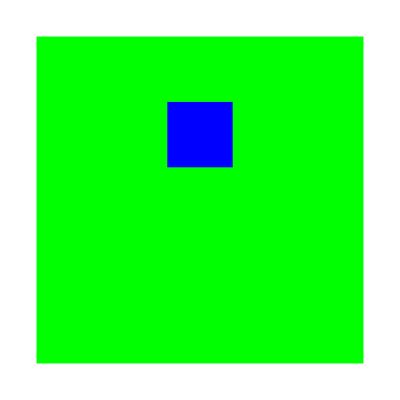

```mathematica
Show[background,antSquare]
```

Perfect! Now let's just step through the ant colony and for each cell, either add an ant, a border cell, or keep it the same color as the background for an empty cell.

### Code

```mathematica
Clear[plotBackground]
plotBackground[size_,color_,opts___]:=
Module[
{},

Show[
Graphics[
{color,Rectangle[{0,0},{size,size}]}],opts,AspectRatio->1]
];
```

Now we'll make a plotCluster function that plots the border as green, an active ant as blue, an inactive ant as black, and an empty site as gray.

```mathematica
Clear[plotCluster]
plotCluster[n_,p_,s_,r_,t_]:=
Module[
{plotAnts,plotBK,size,i,j,plotLattice,a,graphicsList,lattice},

lattice=samsFarm[n,p,s,r,t];

size=Length[lattice[[1]]];
plotBK=plotBackground[size,GrayLevel[0.8],PlotLabel->StringForm["Colony with p = ``, s = ``, r = ``", p ,s,r]];

graphicsList={};

For[a=0,a<t,a++(
plotLattice={};
For[j=1,j≤size,j++,( 
For[i=1,i≤size,i++,( 
If[lattice[[a]][[-j]][[i]][[1]]==b,
AppendTo[plotLattice,Graphics[{Green,Rectangle[{i-1,j-1},{i,j}]}]];
];
If[lattice[[a]][[i]][[-j]][[1]]==-1,
AppendTo[plotLattice,Graphics[{Black,Rectangle[{i-1,j-1},{i,j}]}]];
];
If[lattice[[a]][[i]][[-j]][[1]]==1,
AppendTo[plotLattice,Graphics[{EdgeForm[Thin],Blue,Rectangle[{i-1,j-1},{i,j}]}]];
];
If[lattice[[a]][[i]][[-j]][[1]]==2,
AppendTo[plotLattice,Graphics[{EdgeForm[Thin],Blue,Rectangle[{i-1,j-1},{i,j}]}]];
];
If[lattice[[a]][[i]][[-j]][[1]]==3,
AppendTo[plotLattice,Graphics[{EdgeForm[Thin],Blue,Rectangle[{i-1,j-1},{i,j}]}]];
];
If[lattice[[a]][[i]][[-j]][[1]]==4,
AppendTo[plotLattice,Graphics[{EdgeForm[Thin],Blue,Rectangle[{i-1,j-1},{i,j}]}]];
];
);
]; 
); 
];
AppendTo[graphicsList,{Show[plotBK,plotLattice]}];
);
];
graphicsList
];
```

### Code Test

Let's make sure it works for just a single run of the ant colony farm:

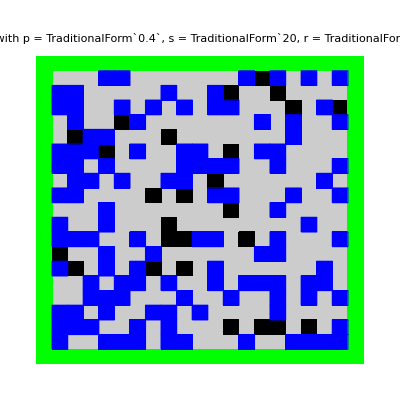

```mathematica
plotCluster[20,0.4,20,0.15,1]
```

Perfect! Now let's try making an animation out of a large number of time steps:

```mathematica
ListAnimate[plotCluster[20,0.1,20,0.15,20]]
```

Great! Now we just need two more different ones for the notebook:

```mathematica
ListAnimate[plotCluster[20,0.3,20,0.15,30]]
```

```mathematica
ListAnimate[plotCluster[20,0.9,20,0.15,30]]
```

## Appendix E: Second Model

The second model is very similar to the first, so we won't go through all of the code development that it took to make the model since it's already in Appendix A. However, we did make one slight change:

### Code Development

The only change to our code is that now, instead of automatically setting the activity time clock of a colony to be a given s value, we will set it to be a randomly chosen number with a probability distribution given by a normal distribution with the mean set at μ=s and the standard deviation as σ=s/5.

```mathematica
dist=NormalDistribution[10,10/5]
```

NormalDistribution[10,2]

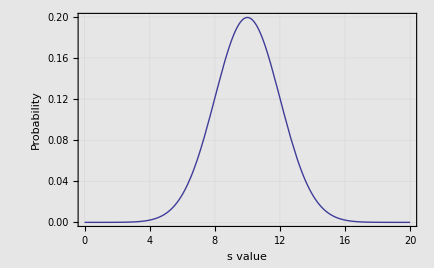

```mathematica
Plot[PDF[dist,x],{x,0,20},Frame->True,PlotStyle->Thick,GridLines->Automatic,FrameLabel->{"s value","Probability","Probability Distribution for s = 10",""},Background->GrayLevel[0.9]]
```

Now that we have this distribution, though, we want to take a random s value with the probability of getting that value determined by the distribution. To do this, we can use the RandomReal[] function, which gets a random real number from a probability distribution

```mathematica
RandomReal[dist]
```

10.1276

Then we want to round it and we're good!

```mathematica
randomSValue=Round[RandomReal[dist]]
```

7

There is one other change that we have to make to the model to accommodate this change in how we determine the activity time clock. Because of the fact that for every ant, its time clock will be different, each ant needs to carry with it the time clock assigned to it at the beginning of the simulation. In the first model, each site on the lattice consisted of the ordered pair {x,s} where x was the direction the ant was facing (or a -1 if inactive, 0 if empty, or b if a border site) and s was the current  activity time clock. Now, each site will have a list of the form {x,a,s}, where x is the same as it was before, a is a negative number counting up from -s to 0 (when it hits 0, the ant becomes inactive), and s is the given activity time clock of the ant which stays constant throughout the simulation. We had to make a negative because of some programming obstacles but it works!

### Code

```mathematica
farm2=samsFarm2[n_,p_,s_,r_,t_]:=
Module[{antPopulation,antFarm,border,ant,randomS,ownS,newPopulation,finalColony},
randomS:=Round[RandomReal[NormalDistribution[s,s/5]]];
antPopulation=
Table[{{-1,1,2,3,4}[[Random[Integer,{1,5}]]],
Random[Integer,{1,ownS=randomS}]-ownS,ownS}* Floor[Random[]+p],
	{n-1},{n-1}]/.{-1,_,x_}->{-1,0,x};

addZeros[list_]:=Prepend[list,Table[{b,0,0},{Length[list[[1]]]}]];

border=Append[Map[Append[#,{b,0,0}]&,#],Table[{b,0,0},{Length[#]+1}]]&;

newPopulation=border[antPopulation];

finalColony=Transpose[addZeros[Transpose[addZeros[newPopulation]]]];

RND:=Random[Integer,{1,4}];

ant[{-1,0,z_},{x_?Positive,_,_},_,_,_,_,_,_,_,_,_,_,_]:={RND,-z,z};
ant[{-1,0,z_},_,{x_?Positive,_,_},_,_,_,_,_,_,_,_,_,_]:={RND,-z,z};
ant[{-1,0,z_},_,_,{x_?Positive,_,_},_,_,_,_,_,_,_,_,_]:={RND,-z,z};
ant[{-1,0,z_},_,_,_,{x_?Positive,_,_},_,_,_,_,_,_,_,_]:={RND,-z,z};

ant[{-1,0,z_},_,_,_,_,_,_,_,_,_,_,_,_]:=
		{ -1+# * Random[Integer,{2,5}],#*(-z),z}&[Floor[Random[]+r]];

ant[{x_?Positive,0,z_},_,_,_,_,_,_,_,_,_,_,_,_]:={-1,0,z};


ant[{1,y_,z_},{-1|x_?Positive|b,_,_},_,_,_,_,_,_,_,_,_,_,_]:={RND,y+1,z};
ant[{2,y_,z_},_,{-1|x_?Positive|b,_,_},_,_,_,_,_,_,_,_,_,_]:={RND,y+1,z};
ant[{3,y_,z_},_,_,{-1|x_?Positive|b,_,_},_,_,_,_,_,_,_,_,_]:={RND,y+1,z};
ant[{4,y_,z_},_,_,_,{-1|x_?Positive|b,_,_},_,_,_,_,_,_,_,_]:={RND,y+1,z};

 ant[{1,y_,z_},{0,0,0},_,_,_,{4,_,_},_,_,_,_,_,_,_]:={RND,y+1,z};
ant[{1,y_,z_},{0,0,0},_,_,_,_,_,_,{2,_,_},_,_,_,_]:={RND,y+1,z};
ant[{1,y_,z_},{0,0,0},_,_,_,_,_,_,_,{3,_,_},_,_,_]:={RND,y+1,z};
ant[{2,y_,z_},_,{0,0,0},_,_,{3,_,_},_,_,_,_,_,_,_]:={RND,y+1,z};
ant[{2,y_,z_},_,{0,0,0},_,_,_,{1,_,_},_,_,_,_,_,_]:={RND,y+1,z};
ant[{2,y_,z_},_,{0,0,0},_,_,_,_,_,_,_,{4,_,_},_,_]:={RND,y+1,z};
ant[{3,y_,z_},_,_,{0,0,0},_,_,{4,_,_},_,_,_,_,_,_]:={RND,y+1,z};
ant[{3,y_,z_},_,_,{0,0,0},_,_,_,{2,_,_},_,_,_,_,_]:={RND,y+1,z};
ant[{3,y_,z_},_,_,{0,0,0},_,_,_,_,_,_,_,{1,_,_},_]:={RND,y+1,z};
ant[{4,y_,z_},_,_,_,{0,0,0},_,_,{1,_,_},_,_,_,_,_]:={RND,y+1,z};
ant[{4,y_,z_},_,_,_,{0,0,0},_,_,_,{3,_,_},_,_,_,_]:={RND,y+1,z};
ant[{4,y_,z_},_,_,_,{0,0,0},_,_,_,_,_,_,_,{2,_,_}]:={RND,y+1,z};

ant[{1,_,_},{0,0,0},_,_,_,_,_,_,_,_,_,_,_]:={0,0,0};
ant[{2,_,_},_,{0,0,0},_,_,_,_,_,_,_,_,_,_]:={0,0,0};
ant[{3,_,_},_,_,{0,0,0},_,_,_,_,_,_,_,_,_]:={0,0,0};
ant[{4,_,_},_,_,_,{0,0,0},_,_,_,_,_,_,_,_]:={0,0,0};

ant[{0,0,0},{3,_,_},{4,_,_},_,_,_,_,_,_,_,_,_,_]:={0,0,0};
ant[{0,0,0},{3,_,_},_,{1,_,_},_,_,_,_,_,_,_,_,_]:={0,0,0};
ant[{0,0,0},{3,_,_},_,_,{2,_,_},_,_,_,_,_,_,_,_]:={0,0,0};
ant[{0,0,0},_,{4,_,_},{1,_,_},_,_,_,_,_,_,_,_,_]:={0,0,0};
ant[{0,0,0},_,{4,_,_},_,{2,_,_},_,_,_,_,_,_,_,_]:={0,0,0};
ant[{0,0,0},_,_,{1,_,_},{2,_,_},_,_,_,_,_,_,_,_]:={0,0,0};

ant[{0,0,0},{3,y_?(#<0&),z_},_,_,_,_,_,_,_,_,_,_,_]:={RND,y+1,z};
ant[{0,0,0},_,{4,y_?(#<0&),z_},_,_,_,_,_,_,_,_,_,_]:={RND,y+1,z};
ant[{0,0,0},_,_,{1,y_?(#<0&),z_},_,_,_,_,_,_,_,_,_]:={RND,y+1,z};
ant[{0,0,0},_,_,_,{2,y_?(#<0&),z_},_,_,_,_,_,_,_,_]:={RND,y+1,z};

ant[{0,0,0},_,_,_,_,_,_,_,_,_,_,_,_]:={0,0,0};
ant[{b,0,0},_,_,_,_,_,_,_,_,_,_,_,_]:={b,0,0};

MvonN[func__,lat_]:=
MapThread[func,Map[RotateRight[lat,#]&,
		{{0,0},{1,0},{0,-1},{-1,0},{0,1},
		{1,-1},{-1,-1},{-1,1},{1,1},
		{2,0},{0,-2},{-2,0},{0,2}}],2];

NestList[MvonN[ant,#]&,finalColony,t]
]
```

### Code Test

```mathematica
samsFarm2[5,0.6,10,0.15,2]//MatrixForm
```

((b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0) | (b | 0 | 0
1 | -7 | 9
1 | -2 | 8
2 | -6 | 12
0 | 0 | 0
b | 0 | 0) | (b | 0 | 0
-1 | 0 | 10
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
b | 0 | 0) | (b | 0 | 0
4 | -5 | 7
-1 | 0 | 10
-1 | 0 | 9
1 | -7 | 12
b | 0 | 0) | (b | 0 | 0
1 | -2 | 10
3 | -7 | 9
0 | 0 | 0
2 | -8 | 10
b | 0 | 0) | (b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0)
(b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0) | (b | 0 | 0
2 | -6 | 9
3 | -1 | 8
0 | 0 | 0
2 | -5 | 12
b | 0 | 0) | (b | 0 | 0
1 | -10 | 10
0 | 0 | 0
0 | 0 | 0
3 | -6 | 12
b | 0 | 0) | (b | 0 | 0
1 | -4 | 7
1 | -10 | 10
1 | -9 | 9
0 | 0 | 0
b | 0 | 0) | (b | 0 | 0
2 | -1 | 10
3 | -6 | 9
0 | 0 | 0
2 | -7 | 10
b | 0 | 0) | (b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0)
(b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0) | (b | 0 | 0
4 | -5 | 9
2 | 0 | 8
0 | 0 | 0
2 | -4 | 12
b | 0 | 0) | (b | 0 | 0
4 | -9 | 10
0 | 0 | 0
1 | -8 | 9
0 | 0 | 0
b | 0 | 0) | (b | 0 | 0
1 | -3 | 7
4 | -9 | 10
0 | 0 | 0
2 | -5 | 12
b | 0 | 0) | (b | 0 | 0
4 | 0 | 10
4 | -5 | 9
0 | 0 | 0
2 | -6 | 10
b | 0 | 0) | (b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0
b | 0 | 0))

Looks like it works! We can see the ants moving around the lattice, with active ants adding 1 to their middle value, the a value, and the activity time clock a little different for every ant but staying constant throughout the simulation. Hooray!

## Appendix F: Results of Second Model

The plot function for the second model is almost identical to the first one so we'll ignore the code development for it and just paste the code:

### Code

```mathematica
plotFunction2[n_,p_,s_,r_,t_,tMin_]:=
Module[
{farm,plot,min,max,range},

SeedRandom[];
farm=Map[Count[Flatten[#,1],{x_?Positive,_,_}]&,
Drop[samsFarm2[n,p,s,r,t],tMin]];

min=Min[farm[[1;;t-tMin]]];
max=Max[farm[[1;;t-tMin]]];
range=max-min;
ListPlot[farm,
		Frame->True,
		PlotJoined->True,
		PlotRange->{{0,t-tMin},{min-range,max+range}},
		PlotStyle->Thick,
		FrameLabel->{"Time Step","Activity",StringForm["Ant Colony Activity with p = ``, s = ``, r = ``",p,s,r],""},
		GridLines->Automatic,
		ImageSize->500,
		Background->GrayLevel[0.9]]

];
```

### Code Runs

Now let's try running the code on a bunch of different situations and varying parameters, just like we did with the first model

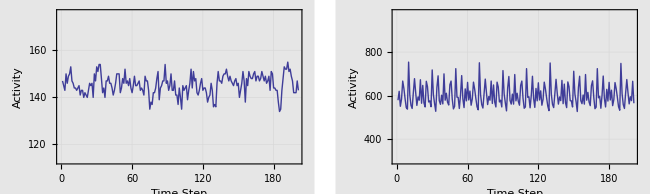

```mathematica
plot01=plotFunction2[30,0.2,20,0.15,250,50];
plot02=plotFunction2[30,0.9,3,0.9,250,50];
GraphicsGrid[{{plot01,plot02}},ImageSize->650]
```

Check out that periodicity! It seems to only happen for more restricted values but we can definitely get periodicity to occur

#### Varying p

Now let's vary the p parameter like we did in the first model to see if we get more consistent periodicity with a higher p value.

```mathematica
plot01p=plotFunction2[20,0.1,3,0.9,250,50];
plot02p=plotFunction2[20,0.2,3,0.9,250,50];
plot03p=plotFunction2[20,0.3,3,0.9,250,50];
plot04p=plotFunction2[20,0.4,3,0.9,250,50];
plot05p=plotFunction2[20,0.5,3,0.9,250,50];
plot06p=plotFunction2[20,0.6,3,0.9,250,50];
plot07p=plotFunction2[20,0.7,3,0.9,250,50];
plot08p=plotFunction2[20,0.8,3,0.9,250,50];
plot09p=plotFunction2[20,0.9,3,0.9,250,50];
plotListP={plot01p,plot02p,plot03p,plot04p,plot05p,plot06p,plot07p,plot08p,plot09p};
```

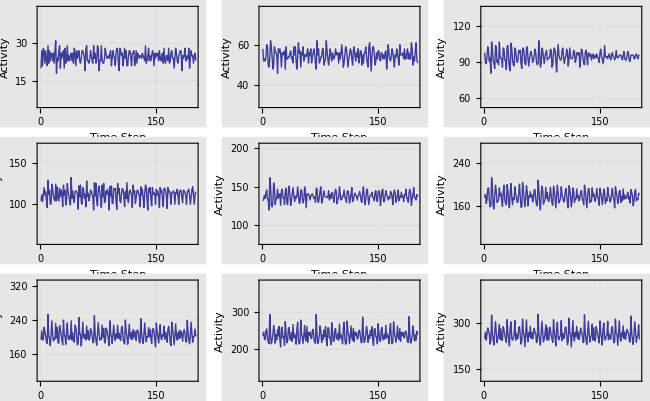

```mathematica
GraphicsGrid[Partition[plotListP,3],ImageSize->650]
```

It looks like we do! The periodicity isn't quite as clear or as distinct as that of the first model, but it is definitely there and it definitely gets progressively stronger with higher p values.

#### Varying s

Now we'll do the same thing with the s parameter

```mathematica
plot01s=plotFunction2[20,0.8,3,0.9,250,50];
plot02s=plotFunction2[20,0.8,10,0.9,250,50];
plot03s=plotFunction2[20,0.8,20,0.9,250,50];
plot04s=plotFunction2[20,0.8,30,0.9,250,50];
plot05s=plotFunction2[20,0.8,40,0.9,250,50];
plot06s=plotFunction2[20,0.8,50,0.9,250,50];
plot07s=plotFunction2[20,0.8,60,0.9,250,50];
plot08s=plotFunction2[20,0.8,70,0.9,250,50];
plot09s=plotFunction2[20,0.8,80,0.9,250,50];
plotListS={plot01s,plot02s,plot03s,plot04s,plot05s,plot06s,plot07s,plot08s,plot09s};
```

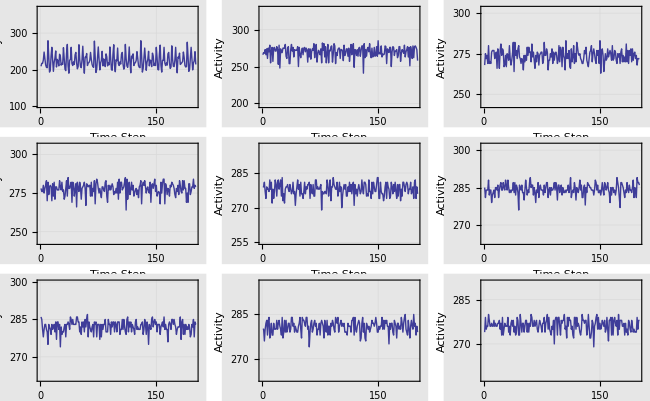

```mathematica
GraphicsGrid[Partition[plotListS,3],ImageSize->650]
```

As we can see, with higher s values we get less and less periodicity... it seems that in order for this model to work, we need a low s value so that the range of possible s values for the ants is not enormous.

#### Varying r

Now let's find out what happens when we produce a range of plots for a large number of different r values

```mathematica
plot01r=plotFunction2[20,0.7,3,0.05,250,50];
plot02r=plotFunction2[20,0.7,3,0.15,250,50];
plot03r=plotFunction2[20,0.7,3,0.35,250,50];
plot04r=plotFunction2[20,0.7,3,0.45,250,50];
plot05r=plotFunction2[20,0.7,3,0.55,250,50];
plot06r=plotFunction2[20,0.7,3,0.65,250,50];
plot07r=plotFunction2[20,0.7,3,0.75,250,50];
plot08r=plotFunction2[20,0.7,3,0.85,250,50];
plot09r=plotFunction2[20,0.7,3,0.95,250,50];
plotListR={plot01r,plot02r,plot03r,plot04r,plot05r,plot06r,plot07r,plot08r,plot09r};
```

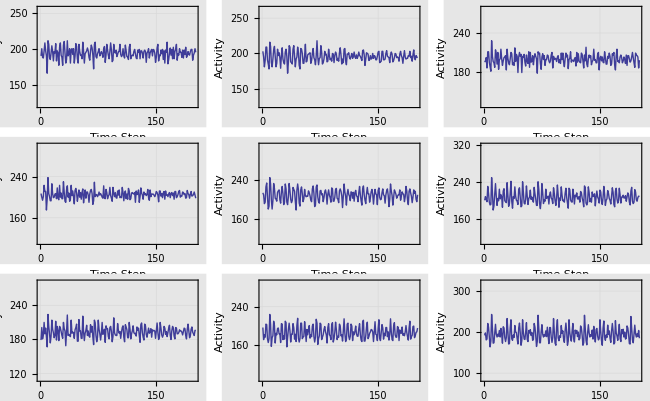

```mathematica
GraphicsGrid[Partition[plotListR,3],ImageSize->650]
```

As we can see, the periodicity clearly increases with a larger r value. This makes a lot of intuitive sense, too, since if ants are almost guaranteed to become active right away, because of the high r value, then organization will occur because the same dips and spikes will occur as the same ants become inactive and then active again.

#### Varying n

Lastly, let's see what sort of effect changing the lattice size has on the periodicity of the activity of an ant colony

```mathematica
plot01n=plotFunction2[10,0.7,3,0.9,250,50];
plot02n=plotFunction2[20,0.7,3,0.9,250,50];
plot03n=plotFunction2[30,0.7,3,0.9,250,50];
plot04n=plotFunction2[40,0.7,3,0.9,250,50];
plot05n=plotFunction2[50,0.7,3,0.9,250,50];
plot06n=plotFunction2[60,0.7,3,0.9,250,50];
plot07n=plotFunction2[70,0.7,3,0.9,250,50];
plot08n=plotFunction2[80,0.7,3,0.9,250,50];
plot09n=plotFunction2[90,0.7,3,0.9,250,50];
plotListN={plot01n,plot02n,plot03n,plot04n,plot05n,plot06n,plot07n,plot08n,plot09n};
```

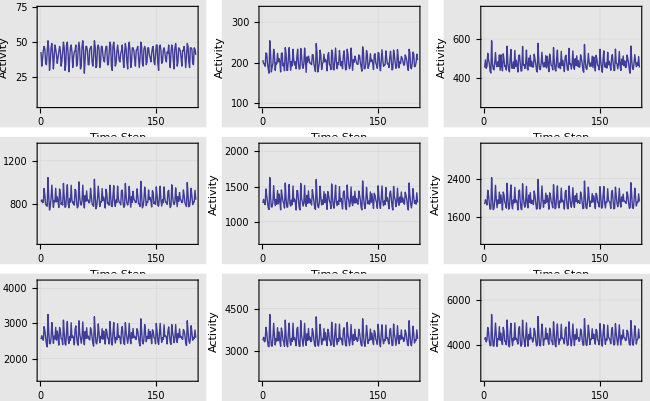

```mathematica
GraphicsGrid[Partition[plotListN,3],ImageSize->650]
```

As was the case with the first model, the different n values don't seem to have an effect on the periodicity as long as the lattice size is greater than 10x10 to ensure that probability is doing its job well enough. The periodicity doesn't seem to be changing throughout the rest of the plots so we can assume that the n value has no effect on the periodicity of the ant colony activity in this second model.

### Animating the Colony

Lastly, we'll just make an animating function that will animate our new colony. The code is almost identical to the previous animating function so we won't go through the code development

#### Code

```mathematica
Clear[plotCluster2]
plotCluster2[n_,p_,s_,r_,t_]:=
Module[
{plotAnts,plotBK,size,i,j,plotLattice,a,graphicsList,lattice},

lattice=samsFarm2[n,p,s,r,t];

size=Length[lattice[[1]]];
plotBK=plotBackground[size,GrayLevel[0.8],PlotLabel->StringForm["Colony with p = ``, s = ``, r = ``", p ,s,r]];

graphicsList={};

For[a=0,a<t,a++(
plotLattice={};
For[j=1,j≤size,j++,( 
For[i=1,i≤size,i++,( 
If[lattice[[a]][[-j]][[i]][[1]]==b,
AppendTo[plotLattice,Graphics[{Green,Rectangle[{i-1,j-1},{i,j}]}]];
];
If[lattice[[a]][[i]][[-j]][[1]]==-1,
AppendTo[plotLattice,Graphics[{Black,Rectangle[{i-1,j-1},{i,j}]}]];
];
If[lattice[[a]][[i]][[-j]][[1]]==1,
AppendTo[plotLattice,Graphics[{EdgeForm[Thin],Blue,Rectangle[{i-1,j-1},{i,j}]}]];
];
If[lattice[[a]][[i]][[-j]][[1]]==2,
AppendTo[plotLattice,Graphics[{EdgeForm[Thin],Blue,Rectangle[{i-1,j-1},{i,j}]}]];
];
If[lattice[[a]][[i]][[-j]][[1]]==3,
AppendTo[plotLattice,Graphics[{EdgeForm[Thin],Blue,Rectangle[{i-1,j-1},{i,j}]}]];
];
If[lattice[[a]][[i]][[-j]][[1]]==4,
AppendTo[plotLattice,Graphics[{EdgeForm[Thin],Blue,Rectangle[{i-1,j-1},{i,j}]}]];
];
);
]; 
); 
];
AppendTo[graphicsList,{Show[plotBK,plotLattice]}];
);
];
graphicsList
];
```

#### Code Test

```mathematica
ListAnimate[plotCluster2[20,0.6,3,0.9,20]]
```

## References

[1] Gaylord, Richard J., and Kazume Nishidate. Modeling Nature. New-York: Springer, 1996. Print.
[2] Gordon, Deborah. Ants at Work: How an Insect Society Is Organized. New York, NY: Free, 1999. Print.
[3] Gordon, Deborah. "Deborah Gordon Digs Ants." TED Talks. Feb 2003.
[4] "Small wonders: What ants can teach us." July 2011. CBS News. Accessed November 2 2011. <http://www.cbsnews.com/stories/2011/07/24/sunday/main20082643.shtml>